# Teubner.f conversion factor

```mathematica
α = 1/137;
teubnerFactor = -3/α
teubner2Gev = -0.005554;
teubner2Gev teubnerFactor
```

-411

2.28269

# Experimental Integral

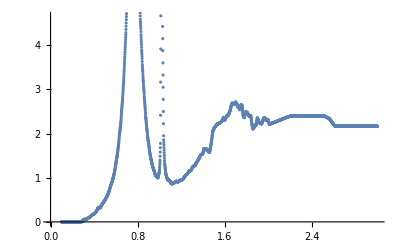

InterpolatingFunction::dmvali: The integration endpoint TraditionalForm`0 in dimension TraditionalForm`1 lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmvali: The integration endpoint TraditionalForm`3 in dimension TraditionalForm`1 lies outside the range of data in the interpolating function. Extrapolation will be used.

6.12525

```mathematica
data = Import["/Users/Knowledge/Developer/ROOT/Experiment/data.dat", "Table"];
ListPlot[data]
Integrate[Interpolation[data,InterpolationOrder->2][x],{x,0,3}]
```